# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Ustable periodic orbits

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun];

F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];


Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];

Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

## Energy surface

```mathematica
Clear[h2M,h2m];
(*h2M[α_,k_,Q_,P_]:=α((1/2)((Q-0.20)^2+P^2)-1)+(k*(Q-0.20)^2)(1-(1/4)((Q-0.20)^2+P^2));*)
h2M[α_,k_,Q_,P_]:=α((1/2)(Q^2+P^2)-1)+(k*Q^2)(1-(1/4)(Q^2+P^2));
```

```mathematica
Clear[α,k];
α=2.1;
k=100α;
Plot3D[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],23,Black],ColorFunction->"WatermelonColors",PlotLegends->Automatic]
```

```mathematica
Clear[α,k];
α=2.1;
k=-100α;
Plot3D[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],23,Black],ColorFunction->"WatermelonColors",PlotLegends->Automatic]
```

```mathematica
surface=ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],50,Black],Contours->100,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,ImageSize->600,GridLines->None,ColorFunction->"LightTerrain"]
```

```mathematica
surface=ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],50,Black],Contours->100,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,ImageSize->600,GridLines->None,ColorFunction->"LightTerrain"]
```

## Poincare differences

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
randomregion=RandomPoint[Disk[{0.5,1},0.4],1000];
(*randomregion=Table[{i,0},{i,0,1.9990,0.0001}];*)
θ=-α/2;
(*randomregion=(rot[θ].#&/@randomregion);*)
randomregionb=-randomregion;
randomregion//Length
```

1000

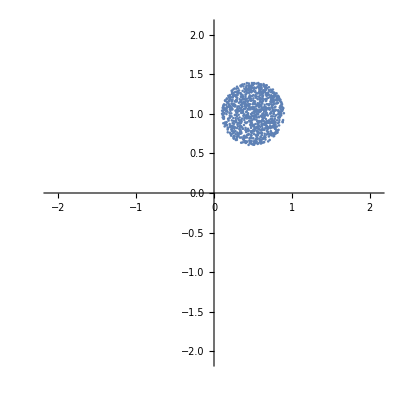

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=100;
k=100α;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
newpoincarea=(rot[θ].#&/@newpoincarea);
poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];

puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregionb}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
newpoincarea=(rot[θ].#&/@newpoincarea);
poincarea=Graphics[{PointSize[0.0025],Black,Opacity[0.2],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,45,Black],Style[", n ="<>ToString[kicks],45,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];
```

```mathematica
Show[poincarea,poincarec,ImageSize->800,PlotRange->{{-2.1,2.1},{-2.1,2.1}}];
Export["poincare_alfa_"<>ToString[α]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>".png",Show[poincarea,poincarec,ImageSize->800,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]];
```

## UPOs

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
randomregion=RandomPoint[Disk[{0,0},1.9999],10];
```

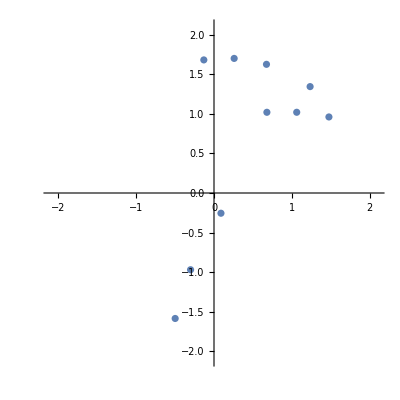

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=1000;
k=1.3;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poicareplot=Graphics[{PointSize[0.0025],Blue,Opacity[0.4],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->500];
```

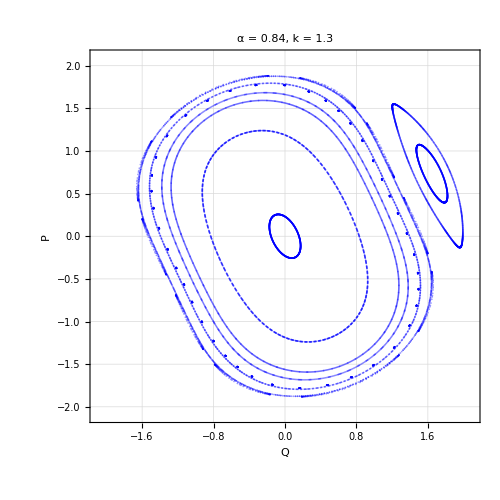

```mathematica
poicareplot
```

```mathematica
mapeo[i,α,k,kicks]
```

```mathematica
(*Standard map definition*)
standardMap[{x_,y_},K_]:=Module[{yn,xn},yn=y+K Sin[x];
xn=Mod[x+yn,2 Pi];
{xn,yn}];

(*Runge-Kutta 4th order step*)
rungeKuttaStep[map_,z_,h_,K_]:=Module[{k1,k2,k3,k4},k1=h map[z,K];
k2=h map[z+0.5 k1,K];
k3=h map[z+0.5 k2,K];
k4=h map[z+k3,K];
z+(k1+2 k2+2 k3+k4)/6];

(*Iterative integration with Runge-Kutta*)
rungeKuttaIterate[map_,z0_,p_,h_,K_]:=Nest[rungeKuttaStep[map,#,h,K]&,z0,p];

(*Objective function for periodic orbits*)
objectiveRK[z0_,p_,h_,K_]:=rungeKuttaIterate[standardMap,z0,p,h,K]-z0;

(*Systematic root finding*)
findPeriodicOrbitsRK[p_,h_,K_,gridSize_]:=Module[{initialGuesses,solutions},initialGuesses=Flatten[Table[{x,y},{x,0,2 Pi,2 Pi/gridSize},{y,0,2 Pi,2 Pi/gridSize}],1];
solutions=Table[FindRoot[objectiveRK[{x,y},p,h,K],{{x,guess[[1]]},{y,guess[[2]]}},Method->"Newton"],{guess,initialGuesses}];
Union[solutions]];

(*Stability analysis*)
stabilityRK[z0_,p_,h_,K_]:=Module[{jacobian,eigenvalues},jacobian=D[rungeKuttaIterate[standardMap,{x,y},p,h,K],{{x,y}}];
eigenvalues=Eigenvalues[jacobian/. Thread[{x,y}->z0]];
eigenvalues];
```

```mathematica
k=1.8;
Δt=0.01;
p=2;
periodicOrbits=findPeriodicOrbitsRK[p,Δt,k,2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
periodicOrbits
```

{{x→-6.28324,y→0.0000889038},{x→-0.000050198,y→0.0000889038},{x→-0.0000109737,y→-0.0000205392},{x→0.,y→0.},{x→0.0000623795,y→-0.000130496},{x→0.0000693116,y→-0.000144999},{x→6.28315,y→0.0000353423},{x→6.28317,y→-0.0000205392},{x→6.28319,y→2.67873×10^-15}}

```mathematica
standardMap[{-6.283235505189737,0.000088903824414914},k]
```

{6.28313,-1.45259×10^-6}

```mathematica
standardMap[{6.283133656575618,-1.4525938173851418*^-6},k]
```

{6.28304,-0.0000944237}

```mathematica
Table[stabilityRK[i,p,Δt,k],{i,periodicOrbits}]
```

$Aborted

## Lagrangian descriptor